```mathematica
Входные данные;
```

```mathematica
ϵ=0.001;α=10;
f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2; X0={-1,-2};
g1[{x_,y_}]:=3(x)^2/4+5(x)/4-2-y;
g2[{x_,y_}]:=3(x)^2/4+5(x)/4-2-y;
(*f[{x_,y_}]:=10 x^2+7 y^2-4x y-4*5^(1/2)(5x- y)-16; X0={0,-5^(1/2)};*)
antiGradF[{x1_,x2_}]:=-Grad[f[{x,y}],{x,y}]/.{x->x1,y->x2};
NormGradF[{x_,y_}]:=Norm[antiGradF[{x,y}]];
uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}]

Clear[κ,ka, kap,X];
```

```mathematica
Метод внутренних штрафных функций;
```

Результат получен за 10 итер.: X = {0.998153, 0.996361}

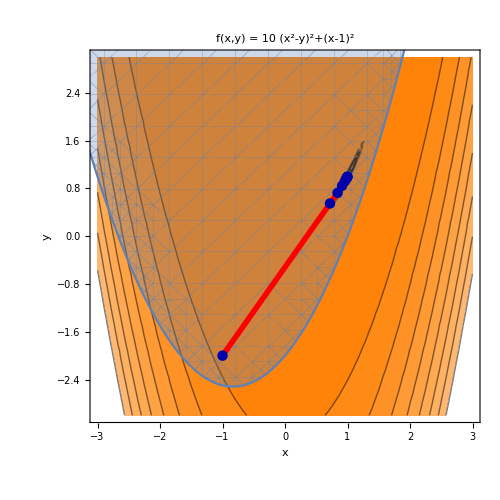

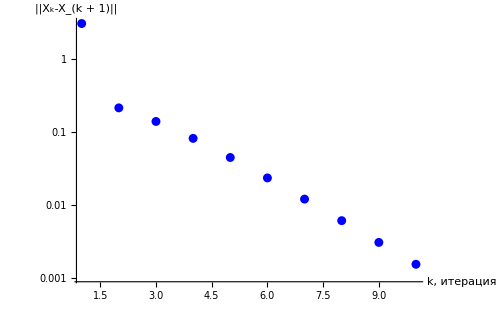

```mathematica
points={X0};fArray={};norm={};X=X0;
r=1;k1=0.5;
f1[{x_,y_}]:=f[{x,y}]-r/g1[{x,y}];
antiGradF1[{x1_,x2_}]:=-Grad[f1[{x,y}],{x,y}]/.{x->x1,y->x2}//N;
NormGradF1[{x_,y_}]:=Norm[antiGradF1[{x,y}]]//N;
While[r>ϵ ,
norm2={NormGradF1[X]};κArr={1};p=antiGradF1[X];κx=10^-3;
While[norm2[[-1]]≥ϵ,
κArr=Append[κArr,κx];
ωArray={};
XOld=X;
X+=κArr[[-1]] p;
ωArray=Append[ωArray,antiGradF1[X]];
p=antiGradF1[X];
norm2=Append[norm2,NormGradF1[X]];
If[f1[XOld]-f1[X]<ωArray[[-1]],κx=2*κx,κx=κx];];
r=k1 r;
norm=Append[norm,Norm[X-points[[-1]]]];
points=Append[points,X];
fArray=Append[fArray,f[X]];
]

(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
"Результат получен за "<>ToString[  Length[points]-1]<> " итер.: X = "<>ToString[X]
CP0={-3,-3};
CP=ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fArray[[1]],0.8(f[CP0]-fArray[[1]]),10]~Join~uniformMesh[fArray[[2]],0.8(fArray[[1]]-fArray[[2]]),2]~Join~fArray[[1;;4]]~Join~{fArray[[3]],fArray[[4]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Red,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}];
RP=RegionPlot[g1[{x,y}]≤0,{x,-5,5},{y,-5,5}];
Show[CP,RP]
ListLogPlot[norm,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||X_k-X_(k + 1)||"}]
```

```mathematica
Метод внешних штрафных функций;
```

Результат получен за 10 итер.: X = {0.998883, 0.997723}

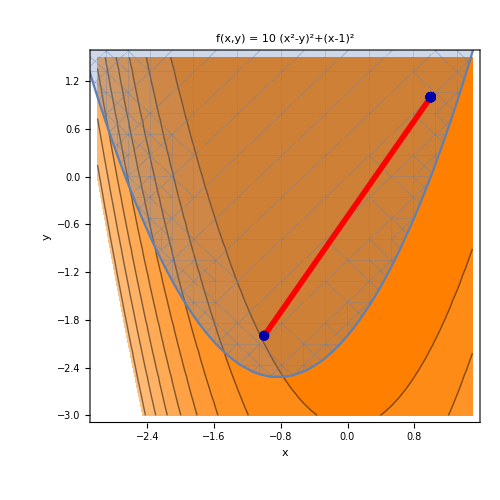

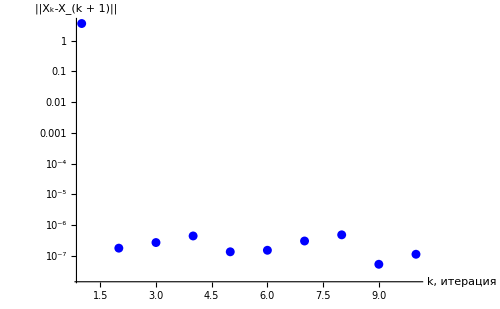

```mathematica
points={X0};fArray={};norm={};X=X0;r=1;k2=2;
f2[{x_,y_}]:=f[{x,y}]+r(Max[g2[{x,y}],0])^2;
antiGradF2[{x1_,x2_}]:=-Grad[f2[{x,y}],{x,y}]/.{x->x1,y->x2}//N;
NormGradF2[{x_,y_}]:=Norm[antiGradF2[{x,y}]]//N;
While[r<1000,

norm2={NormGradF1[X]};κArr={1};p=antiGradF1[X];κx=10^-3;
While[norm2[[-1]]≥ϵ,
κArr=Append[κArr,κx];
ωArray={};
XOld=X;
X+=κArr[[-1]] p;
ωArray=Append[ωArray,antiGradF2[X]];
p=antiGradF2[X];
norm2=Append[norm2,NormGradF2[X]];
If[f1[XOld]-f1[X]<ωArray[[-1]],κx=2*κx,κx=κx];];
r=k2 r;
norm=Append[norm,Norm[X-points[[-1]]]];
points=Append[points,X];
fArray=Append[fArray,f[X]];
];



(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
"Результат получен за "<>ToString[ Length[points]-1]<> " итер.: X = "<>ToString[X]
CP0={-3,-3};
CP=ContourPlot[f[{x,y}],{x,CP0[[1]],1.5},{y,CP0[[1]],1.5},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Red,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}];
RP=RegionPlot[g1[{x,y}]≤0,{x,-5,5},{y,-5,5}];
Show[CP,RP]
ListLogPlot[norm,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||X_k-X_(k + 1)||"}]
```

```mathematica
points
```

{{-1,-2},{0.998883,0.997723},{0.998883,0.997723},{0.998883,0.997723},{0.998883,0.997722},{0.998883,0.997723},{0.998883,0.997722},{0.998883,0.997723},{0.998883,0.997723},{0.998883,0.997723},{0.998883,0.997723}}